#### Function for correcting the alpha angle due to not perfectly putting PS at the outer edges

```mathematica
alphafunc=Function[{y},180/π*ArcCos[(25^2+y^2+2*25^2-(25-y)^2)/(2*√2*25*√(25^2+y^2))]];
alphacorr=alphafunc[16.8]
```

11.0989

#### Data input - all channels [corr_PSL5: new improv base, 4deg, no smooth --> large intw (-20 +10), correction selection with small PS, 4° rotation considered, no smoothing]

```mathematica
LSPosition={"C1","C2","R0","R1","R2","L0","L1","L2"};
Phi={-138,57.26,-56.78,-101.8,3.695,142.4,179.5-360,98.78};
PhiError={0.4,0.53,1.06,0.8,1.061,2.5,0.7,0.69};
Sigma={42.77,47.62,63.82,57.9,68.93,57.51,60.85,53.86};
SigmaError={0.46,0.64,1.91,1.2,2.46,0.98,1.12,0.95};
Radius=1;
Alpha={-135,45,-45,-90-alphacorr,0+alphacorr,135,-180+alphacorr,90-alphacorr}

PhiList=Table[{Phi[[i]]*Pi/180,Radius},{i,Length[Phi]}] ;(*converting to radian and giving a fixed radius*)
LSPositionL=Thread[{LSPosition,Large}];
```

{-135,45,-45,-101.099,11.0989,135,-168.901,78.9011}

```mathematica
Mean[Table[Around[Sigma[[n]],SigmaError[[n]]],{n,1,8}]]
```

56.70.5

```mathematica
Mean[Table[Around[Sigma[[n]],SigmaError[[n]]],{n,1,8}]](*old timing cuts: 2.7, -2.7*)
```

57.71.0

#### Data input - even channels [corr_PSL5: new improv base, 4deg, no smooth --> large intw (-20 +10), correction selection with small PS, 4° rotation considered, no smoothing]

```mathematica
LSPosition={"C1","C2","R0","R1","R2","L0","L1","L2"};
Phi={-136.5,54.55,-76.75,-116.5,-15.65,160.4,191.3-360,99.39};
PhiError={0.7,1.12,1.96,1.2,3.12,1.7,1.3,1.6};
Sigma={56.97,66.59,54.37,69.54,61.52,80.75,83.61,55.73};
SigmaError={1.04,2.26,2.90,2.94,5.76,6.54,7.31,2.38};
Radius=1;
Alpha={-135,45,-45,-90-alphacorr,0+alphacorr,135,-180+alphacorr,90-alphacorr}

PhiList=Table[{Phi[[i]]*Pi/180,Radius},{i,Length[Phi]}] ;(*converting to radian and giving a fixed radius*)
LSPositionL=Thread[{LSPosition,Large}];
```

{-135,45,-45,-101.099,11.0989,135,-168.901,78.9011}

```mathematica
Mean[Table[Around[Sigma[[n]],SigmaError[[n]]],{n,1,8}]]
```

66.11.6

```mathematica
Mean[Table[Around[Sigma[[n]],SigmaError[[n]]],{n,1,8}]](*old timing cuts: 2.7, -2.7*)
```

77.81.5

#### Data input - odd channels [corr_PSL5: new improv base, 4deg, no smooth --> large intw (-20 +10), correction selection with small PS, 4° rotation considered, no smoothing]

```mathematica
LSPosition={"C1","C2","R0","R1","R2","L0","L1","L2"};
Phi={-138.7,57.75,-47.62,-91.28,7.729,137.6,172.6-360,98.9};
PhiError={0.5,0.56,1.09,0.95,1.035,0.7,0.8,0.7};
Sigma={45.43,47.86,76.53,52.24,74.17,59.29,61.15,53.83};
SigmaError={0.58,0.7,3.5,1.31,3.03,1.03,1.26,0.98};
Radius=1;
Alpha={-135,45,-45,-90-alphacorr,0+alphacorr,135,-180+alphacorr,90-alphacorr}

PhiList=Table[{Phi[[i]]*Pi/180,Radius},{i,Length[Phi]}] ;(*converting to radian and giving a fixed radius*)
LSPositionL=Thread[{LSPosition,Large}];
```

{-135,45,-45,-101.099,11.0989,135,-168.901,78.9011}

```mathematica
Mean[Table[Around[Sigma[[n]],SigmaError[[n]]],{n,1,8}]]
```

58.80.7

```mathematica
Mean[Table[Around[Sigma[[n]],SigmaError[[n]]],{n,1,8}]](*old timing cuts: 2.7, -2.7*)
```

59.21.1

#### Data input [data from andrea; corr1ns_new, no smooth, big intw]

```mathematica
LSPosition={"C1","C2","R0","R1","R2","L0","L1","L2"};
Phi={-125.7,36.6,-44.65,-82.73,-17.09,135.2,-183.4,99.32};
PhiError={0.6,0.7,2.20,1.00,1.00,1.6,0.8,0.92};
Sigma={49.59,53.31,56.02,58.74,57.1,51.05,56.2,57.16};
SigmaError={0.68,0.96,2.98,1.59,1.6,2.01,1.1,1.34};
Radius=1;
Alpha={-135,45,-45,-90,0,135,-180,90}

PhiList=Table[{Phi[[i]]*Pi/180,Radius},{i,Length[Phi]}] ;(*converting to radian and giving a fixed radius*)
LSPositionL=Thread[{LSPosition,Large}];
```

{-135,45,-45,-90,0,135,-180,90}

```mathematica
Mean[Table[Around[Sigma[[n]],SigmaError[[n]]],{n,1,8}]]
```

54.90.6

```mathematica
Mean[Table[Around[Sigma[[n]],SigmaError[[n]]],{n,1,8}]] (*old timing cuts: 2.7, -2.7*)
```

53.10.7

### Plotting of the polar plot

```mathematica
PhiPolarPlot=ListPolarPlot[List /@ PhiList, PlotMarkers->List/@LSPositionL,PolarAxes->Automatic,PolarAxesOrigin->{0,Radius+0.2}, PolarTicks->{"Degrees",Automatic},TicksStyle->Medium,PlotRange->1.5,PolarGridLines->Automatic,PlotLabel->Style[TraditionalForm[HoldForm["Corrected " OverBar[Subscript[ϕ,ew]]"[°]"]],Large],ImageSize->Large]
```

-Graphics-

### Plotting of the α-ϕ-Plot

{{-135,-139.45.},{45,58.48.},{-45,-48.77.},{-101.099,-89.56.},{11.0989,7.77.},{135,138.59.},{-168.901,-187.61.},{78.9011,99.54.}}

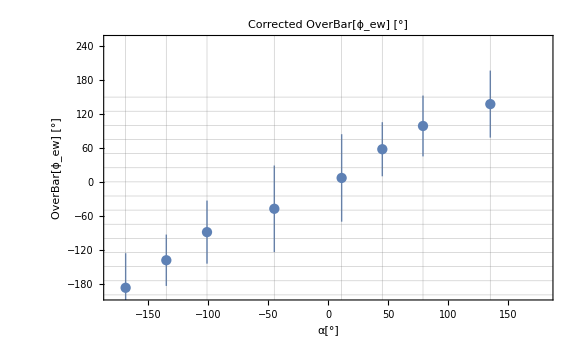

```mathematica
GridList=Table[i*25,{i,-200/25,150/25}];(*only for the graphic*)
AlphaPhiList=Table[{Alpha[[i]],Around[Phi[[i]],Sigma[[i]]]},{i,Length[Phi]}]
AlphaPhiPlot=ListPlot[AlphaPhiList,PlotRange->{{-180,180},{-200,250}},GridLines->{Alpha,GridList}, Axes->False,Frame->True, FrameTicksStyle->Medium, FrameLabel->{Style["α[°]",FontSize->16],Style[TraditionalForm[HoldForm[OverBar[Subscript[ϕ,ew]]"[°]"]],FontSize->16]},PlotLabel->Style[TraditionalForm[HoldForm["Corrected "OverBar[Subscript[ϕ,ew]]"[°]"]],Large], ImageSize->Large]
```

### Plotting the α-σ-Plot

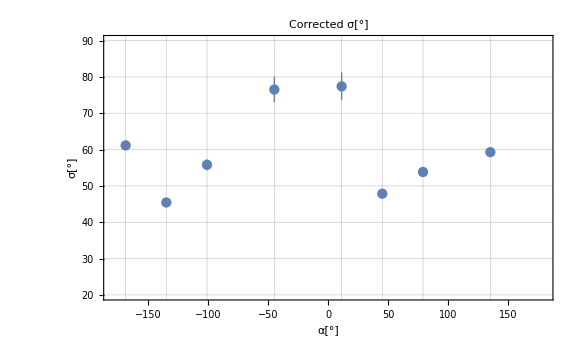

```mathematica
GridList=Table[i*10,{i,-200/25,150/10}];(*only for the graphic*)
AlphaSigmaList=Table[{Alpha[[i]],Around[Sigma[[i]],SigmaError[[i]]]},{i,Length[Sigma]}];
AlphaSigmaPlot=ListPlot[AlphaSigmaList,PlotRange->{{-180,180},{20,90}},GridLines->{Alpha,GridList}, Axes->False,Frame->True,FrameLabel->{"α[°]","σ[°]"},PlotLabel->Style["Corrected σ[°]",Large], ImageSize->Large]
```

## Klarifizierung des Konfidenzintervalls

{{-135,-138.7},{45,57.75},{-45,-47.62},{-101.099,-88.94},{11.0989,6.946},{135,137.6},{-168.901,-187.4},{78.9011,98.9}}

FittedModel[4.74652+1.07168 α]

4.74652+1.07168 α-2.44691 √(1.06789+0.000251991 α+5.64713×10^-6 α^2)

4.74652+1.07168 α+2.44691 √(1.06789+0.000251991 α+5.64713×10^-6 α^2)

-6.78692

-2.07011

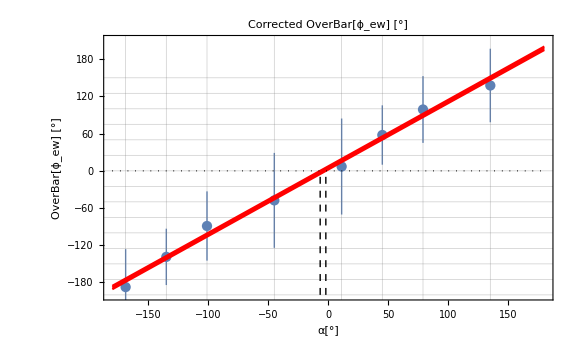

```mathematica
GridList=Table[i*25,{i,-200/25,150/25}];(*only for the graphic*)AlphaPhiPlot=ListPlot[AlphaPhiList,PlotRange->{{-180,180},{-200,210}},GridLines->{Alpha,GridList}, Axes->False,Frame->True,FrameLabel->{"α[°]",TraditionalForm[HoldForm[OverBar[Subscript[ϕ,ew]]"[°]"]]},PlotLabel->Style[TraditionalForm[HoldForm["Corrected "OverBar[Subscript[ϕ,ew]]"[°]"]],Large],ImageSize->Large];
AlphaPhiFitList=Table[{Alpha[[i]],Phi[[i]]},{i,Length[Phi]}]
fit=LinearModelFit[AlphaPhiFitList,α,α,Weights->1/PhiError^2,VarianceEstimatorFunction->(1&)]
LowerPredictionBand=fit["SinglePredictionBands"][[1]]
UpperPredictionBand=fit["SinglePredictionBands"][[2]]

AssumedPhi=0;
MinimumAlpha=Solve[UpperPredictionBand==AssumedPhi,α][[1,1,2]]
MaximumAlpha=Solve[LowerPredictionBand==AssumedPhi,α][[1,1,2]]

ErrorGraphic=Show[AlphaPhiPlot,
Plot[{fit["BestFit"],fit["SinglePredictionBands"]},{α,-180,180},PlotStyle->Red,Filling->{2->{1},3->{1}}],
Graphics[{Dashed,Line[{{MinimumAlpha,-200},{MinimumAlpha,AssumedPhi}}]}],
Graphics[{Dashed,Line[{{MaximumAlpha,-200},{MaximumAlpha,AssumedPhi}}]}],
Graphics[{Dotted,Line[{{-180,0},{180,0}}]}]]
(*Export["/home/alex/Dokumente/Studium/RootReader/RootAnalysis/couplingCorrection/ConfidencePlot.pdf",ErrorGraphic,"PDF"]*)
```

## Klarifizierung des Konfidenzintervalls 2

FittedModel[4.74652+1.07168 α]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 4.74652 | 0.260556 | 18.2169 | 1.76209×10^-6
α | 1.07168 | 0.00237637 | 450.974 | 8.02344×10^-15

| DF | SS | MS | F-Statistic | P-Value
α | 1 | 203378. | 203378. | 1188.23 | 3.97067×10^-8
Error | 6 | 1026.96 | 171.161 |  | 
Total | 7 | 204405. |  |  |

0.994138

59.6612

11.9035

-59.1913+1.07168 α

68.6844+1.07168 α

-64.0903

55.2322

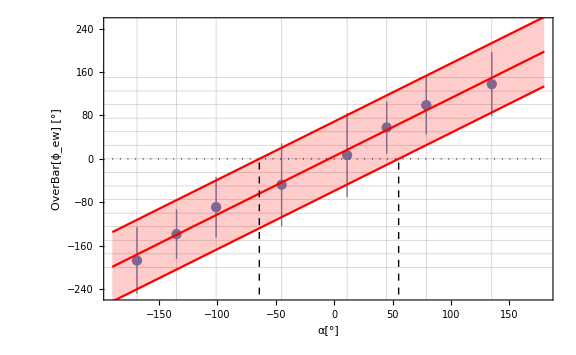

```mathematica
AlphaPhiPlot=ListPlot[AlphaPhiList,PlotRange->{{-190,180},{-250,250}},GridLines->{Alpha,GridList}, Axes->False,Frame->True,FrameTicksStyle->Medium,FrameLabel-> {Style["α[°]",FontSize->16],Style[TraditionalForm[HoldForm[OverBar[Subscript[ϕ,ew]]"[°]"]],FontSize->16]},PlotLabel->Style[TraditionalForm[HoldForm["Corrected "OverBar[Subscript[ϕ,ew]]"[°]"]],Large],ImageSize->Large];
AlphaPhiFitList=Table[{Alpha[[i]],Phi[[i]]},{i,Length[Phi]}];
fit=LinearModelFit[AlphaPhiFitList,α,α,Weights->1/PhiError^2,VarianceEstimatorFunction->(1&)]
fit["ParameterTable"]
fit["ANOVATable"]
fit["AdjustedRSquared"]
MeanSigma=Mean[Sigma]
StandardDeviation[Sigma]
LowerPredictionBand=fit["BestFit"];
UpperPredictionBand=fit["BestFit"];
LowerPredictionBand=LowerPredictionBand-fit["BestFitParameters"][[2]]*MeanSigma
UpperPredictionBand=UpperPredictionBand+fit["BestFitParameters"][[2]]*MeanSigma

AssumedPhi=0;
MinimumAlpha=Solve[UpperPredictionBand==AssumedPhi,α][[1,1,2]]
MaximumAlpha=Solve[LowerPredictionBand==AssumedPhi,α][[1,1,2]]

ErrorGraphic=Show[ListPlot[AlphaPhiList,PlotRange->{{-190,180},{-250,250}},GridLines->{Alpha,GridList}, Axes->False,Frame->True,FrameTicksStyle->Medium,FrameLabel-> {Style["α[°]",FontSize->16],Style[TraditionalForm[HoldForm[OverBar[Subscript[ϕ,ew]]"[°]"]],FontSize->16]},ImageSize->Large],
Plot[{fit["BestFit"],LowerPredictionBand,UpperPredictionBand},{α,-190,180},PlotStyle->Red,Filling->{2->{1},3->{1}}],
Graphics[{Dashed,Line[{{MinimumAlpha,-250},{MinimumAlpha,AssumedPhi}}]}],
Graphics[{Dashed,Line[{{MaximumAlpha,-250},{MaximumAlpha,AssumedPhi}}]}],
Graphics[{Dotted,Line[{{-190,0},{180,0}}]}],
PlotLabels->"Expressions"]
```